```mathematica
Examples of Electric fields E and corresponding vector potentials A:
```

```mathematica
Definition of the electric field profiles:
```

```mathematica
A=.;t0=.;t1=.;ω=.;τ=.;Ω=.
Ef[t_]:=A*Cos[ω*(t-t0)]*Exp[-((t-t0)^2)/(2*τ^2)]
Econstant[t_]:=A*HeavisideTheta[t-t0]*HeavisideTheta[t1-t]
Ramp[t_]:=(1/2-3/4*Cos[π*t/t0]+1/4*Cos[π*t/t0]^3)
Esmooth[t_]:=A*Ramp[t]*HeavisideTheta[t0-t]+Econstant[t]
Ecos[t_]:= A*Cos[Ω*(t-t0)]
```

```mathematica
Get the corresponding vector potential by indefinite integration :
```

```mathematica
FullSimplify[Integrate[Ef[t],t]]
FullSimplify[Integrate[Econstant[t],t]]
FullSimplify[Integrate[Esmooth[t],t]]
FullSimplify[Integrate[Ecos[t],t]]
```

1/2 A ⅇ^(-1/2 τ^2 ω^2) √(π/2) τ (Erf[(t-t0-ⅈ τ^2 ω)/(√2 τ)]+Erf[(t-t0+ⅈ τ^2 ω)/(√2 τ)])

A HeavisideTheta[t-t0] (t-t0+(-t+t1) HeavisideTheta[t-t1]+(t0-t1) HeavisideTheta[t0-t1])

1/(48 π)A (24 π (t+(t-t0) HeavisideTheta[t-t0]+2 (-t+t1) HeavisideTheta[t-t0,t-t1]+2 (t0-t1) HeavisideTheta[t-t0,t0-t1])+27 t0 (-1+HeavisideTheta[t-t0]) Sin[(π t)/t0]-t0 (-1+HeavisideTheta[t-t0]) Sin[(3 π t)/t0])

(A Sin[(t-t0) Ω])/Ω

```mathematica
Copy/Paste Vector potential to new functions:
```

```mathematica
Af[t_]:=1/2 A ⅇ^(-1/2 τ^2 ω^2) √(π/2) τ (Erf[(t-t0-ⅈ τ^2 ω)/(√2 τ)]+Erf[(t-t0+ⅈ τ^2 ω)/(√2 τ)])
Aconstant[t_]:=A HeavisideTheta[t-t0] (t-t0+(-t+t1) HeavisideTheta[t-t1]+(t0-t1) HeavisideTheta[t0-t1])
Asmooth[t_]:=1/(48 π)A (24 π (t+(t-t0) HeavisideTheta[t-t0]+2 (-t+t1) HeavisideTheta[t-t0,t-t1]+2 (t0-t1) HeavisideTheta[t-t0,t0-t1])+27 t0 (-1+HeavisideTheta[t-t0]) Sin[(π t)/t0]-t0 (-1+HeavisideTheta[t-t0]) Sin[(3 π t)/t0])
Acos[t_]:=(A Sin[(t-t0) Ω])/Ω
```

```mathematica
Set specific value of the parametrs appearing in equations above :
```

```mathematica
A=1 ;
t0=π;
 t1=4 ; 
ω=30 ;
 τ=1.0/(2π);
```

```mathematica
Plot  of impulse - like profile :
```

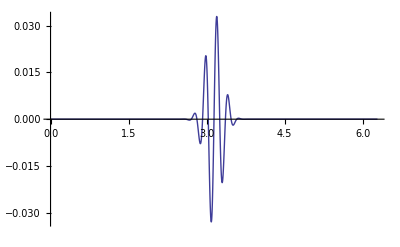

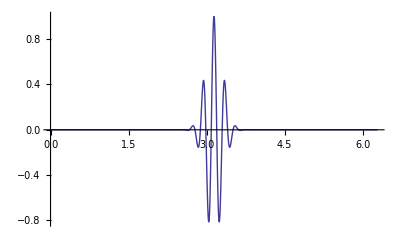

```mathematica
Plot[Re[Af[x]],{x,0,2π},PlotRange->Full]
Plot[Ef[x],{x,0,2π},PlotRange->Full]
```

```mathematica
A=.;t0=.;t1=.;ω=.;τ=.;Ω=.;
```

```mathematica
Plot of the constant profile :
```

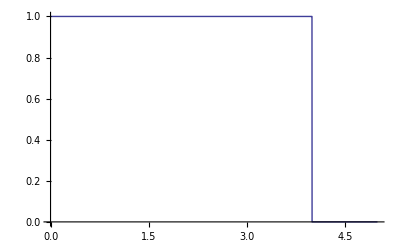

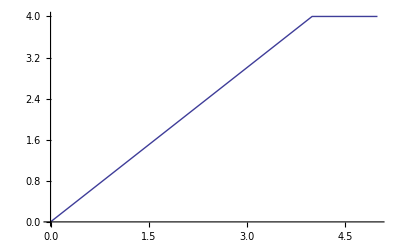

```mathematica
A=1;t0=0;t1=4;
Plot[Econstant[x],{x,0,5},PlotRange->Full]
Plot[Re[Aconstant[x]],{x,0,5},PlotRange->Full]
```

```mathematica
A=.;t0=.;t1=.;ω=.;τ=.;Ω=.;
```

```mathematica
Plot of the ramp profile :
```

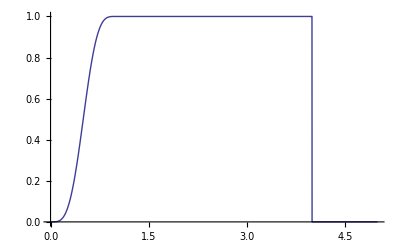

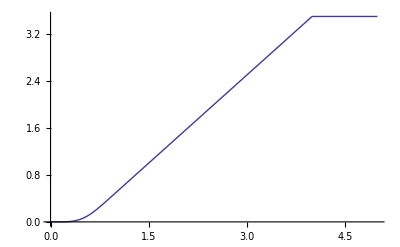

```mathematica
A=1;t0=1;t1=4;
Plot[Esmooth[x],{x,0,5},PlotRange->Full]
Plot[Re[Asmooth[x]],{x,0,5},PlotRange->Full]
```

```mathematica
A=.;t0=.;t1=.;ω=.;τ=.;Ω=.;
```

```mathematica
Plot of the Cos profile :
```

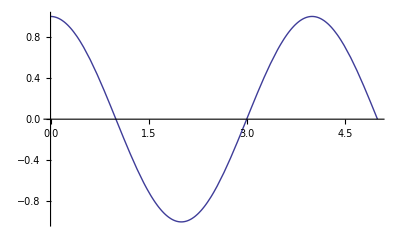

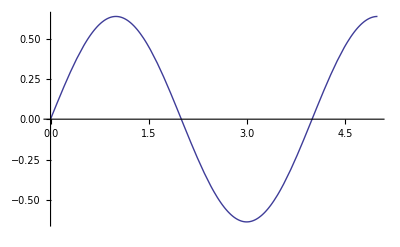

```mathematica
A=1;t0=0;Ω=1π/2;
Plot[Ecos[x],{x,0,5},PlotRange->Full]
Plot[Re[Acos[x]],{x,0,5},PlotRange->Full]
```